```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/TiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/TiSamp/src

```mathematica
data = Import["phitime.txt","CSV"]
```

{{2500,1},{2600,1},{2700,1},{2800,1},{2900,1},{3000,1},{3100,1},{3200,1},{3300,1},{3400,1},{3500,1},{3600,0.666667},{3700,0.666667},{3800,0.75},{3900,0.75},{4000,0.75},{4100,0.75},{4200,0.75},{4300,0.75},{4400,0.75},{4500,0.75},{4600,0.75},{4700,0.75},{4800,0.6},{4900,0.6},{5000,0.6},{5100,0.6},{5200,0.5},{5300,0.571429},{5400,0.571429},{5500,0.625},{5600,0.555556},{5700,0.555556},{5800,0.555556},{5900,0.5},{6000,0.454545},{6100,0.454545},{6200,0.416667},{6300,0.416667},{6400,0.416667},{6500,0.461538},{6600,0.461538},{6700,0.461538},{6800,0.461538},{6900,0.461538},{7000,0.461538},{7100,0.461538},{7200,0.5},{7300,0.5},{7400,0.5},{7500,0.5},{7600,0.5},{7700,0.5},{7800,0.5},{7900,0.5},{8000,0.5},{8100,0.5},{8200,0.466667},{8300,0.4375},{8400,0.4375},{8500,0.4375},{8600,0.4375},{8700,0.411765},{8800,0.444444},{8900,0.444444},{9000,0.444444},{9100,0.444444},{9200,0.444444},{9300,0.444444},{9400,0.444444},{9500,0.473684},{9600,0.45},{9700,0.478261},{9800,0.5},{9900,0.5},{10000,0.5},{10100,0.518519},{10200,0.535714},{10300,0.517241},{10400,0.517241},{10500,0.548387},{10600,0.5625},{10700,0.545455},{10800,0.529412},{10900,0.529412},{11000,0.529412},{11100,0.529412},{11200,0.542857},{11300,0.542857},{11400,0.542857},{11500,0.540541},{11600,0.552632},{11700,0.55},{11800,0.547619},{11900,0.547619},{12000,0.547619},{12100,0.547619},{12200,0.534884},{12300,0.534884},{12400,0.534884},{12500,0.522727},{12600,0.522727},{12700,0.522727},{12800,0.522727},{12900,0.511111},{13000,0.5},{13100,0.5},{13200,0.489362},{13300,0.489362},{13400,0.5},{13500,0.489796},{13600,0.489796},{13700,0.489796},{13800,0.489796},{13900,0.489796},{14000,0.489796},{14100,0.48},{14200,0.480769},{14300,0.471698},{14400,0.462963},{14500,0.462963},{14600,0.462963},{14700,0.462963},{14800,0.464286},{14900,0.491525},{15000,0.508197},{15100,0.5},{15200,0.5},{15300,0.5},{15400,0.484375},{15500,0.484375},{15600,0.484375},{15700,0.492308},{15800,0.492308},{15900,0.492308},{16000,0.492537},{16100,0.492537},{16200,0.478261},{16300,0.478261},{16400,0.471429},{16500,0.478873},{16600,0.486111},{16700,0.486111},{16800,0.486111},{16900,0.493151},{17000,0.493151},{17100,0.486486},{17200,0.486486},{17300,0.486486},{17400,0.486486},{17500,0.48},{17600,0.473684},{17700,0.473684},{17800,0.473684},{17900,0.467532},{18000,0.467532},{18100,0.467532},{18200,0.467532},{18300,0.467532},{18400,0.474359},{18500,0.475},{18600,0.481481},{18700,0.481481},{18800,0.487805},{18900,0.487805},{19000,0.487805},{19100,0.493976},{19200,0.493976},{19300,0.494118},{19400,0.488372},{19500,0.488372},{19600,0.488372},{19700,0.488372},{19800,0.482759},{19900,0.494382},{20000,0.5},{20100,0.505495},{20200,0.51087},{20300,0.505376},{20400,0.5},{20500,0.505263},{20600,0.505263},{20700,0.505263},{20800,0.505263},{20900,0.505263},{21000,0.5},{21100,0.5},{21200,0.505155},{21300,0.505155},{21400,0.5},{21500,0.505051},{21600,0.505051},{21700,0.519608},{21800,0.514563},{21900,0.519231},{22000,0.52381},{22100,0.528302},{22200,0.528302},{22300,0.528302},{22400,0.528302},{22500,0.528302},{22600,0.53271},{22700,0.53211},{22800,0.527273},{22900,0.527273},{23000,0.527273},{23100,0.527273},{23200,0.527273},{23300,0.527273},{23400,0.527273},{23500,0.527273},{23600,0.526786},{23700,0.526786},{23800,0.526786},{23900,0.526786},{24000,0.526316},{24100,0.526316},{24200,0.525862},{24300,0.525862},{24400,0.525862},{24500,0.529915},{24600,0.525424},{24700,0.529412},{24800,0.529412},{24900,0.529412},{25000,0.520661},{25100,0.520661},{25200,0.516393},{25300,0.524194},{25400,0.524194},{25500,0.528},{25600,0.515385},{25700,0.519084},{25800,0.515152},{25900,0.518797},{26000,0.525926},{26100,0.525926},{26200,0.525547},{26300,0.532374},{26400,0.532374},{26500,0.524823},{26600,0.528169},{26700,0.528169},{26800,0.524476},{26900,0.520833},{27000,0.524138},{27100,0.513514},{27200,0.513514},{27300,0.513514},{27400,0.510067},{27500,0.506667},{27600,0.506579},{27700,0.503268},{27800,0.506494},{27900,0.5},{28000,0.496815},{28100,0.493671},{28200,0.490683},{28300,0.490683},{28400,0.490798},{28500,0.490798},{28600,0.490798},{28700,0.490798},{28800,0.493976},{28900,0.488095},{29000,0.488095},{29100,0.491124},{29200,0.491124},{29300,0.491124},{29400,0.488235},{29500,0.491228},{29600,0.494186},{29700,0.491329},{29800,0.497143},{29900,0.497175},{30000,0.5},{30100,0.494444},{30200,0.494444},{30300,0.497238},{30400,0.5},{30500,0.497268},{30600,0.497268},{30700,0.497268},{30800,0.5},{30900,0.502703},{31000,0.505376},{31100,0.505376},{31200,0.502674},{31300,0.502674},{31400,0.505319},{31500,0.502646},{31600,0.502618},{31700,0.5},{31800,0.497409},{31900,0.5},{32000,0.5},{32100,0.497436},{32200,0.497462},{32300,0.502513},{32400,0.502513},{32500,0.5},{32600,0.502488},{32700,0.502488},{32800,0.5},{32900,0.5},{33000,0.502439},{33100,0.502439},{33200,0.502415},{33300,0.504808},{33400,0.504808},{33500,0.507042},{33600,0.506977},{33700,0.506912},{33800,0.506849},{33900,0.506787},{34000,0.509009},{34100,0.511211},{34200,0.511211},{34300,0.515556},{34400,0.513158},{34500,0.513043},{34600,0.513043},{34700,0.517241},{34800,0.521368},{34900,0.519149},{35000,0.516949},{35100,0.516949},{35200,0.516949},{35300,0.516807},{35400,0.516667},{35500,0.514523},{35600,0.512295},{35700,0.512195},{35800,0.512195},{35900,0.514056},{36000,0.50996},{36100,0.50996},{36200,0.507937},{36300,0.507937},{36400,0.511811},{36500,0.513725},{36600,0.515625},{36700,0.515625},{36800,0.513619},{36900,0.513619},{37000,0.517241},{37100,0.519084},{37200,0.519084},{37300,0.520913},{37400,0.520755},{37500,0.518797},{37600,0.518797},{37700,0.516854},{37800,0.513011},{37900,0.511111},{38000,0.511111},{38100,0.511111},{38200,0.507353},{38300,0.507353},{38400,0.505495},{38500,0.50365},{38600,0.501818},{38700,0.501805},{38800,0.503597},{38900,0.501779},{39000,0.503546},{39100,0.503521},{39200,0.503521},{39300,0.505263},{39400,0.506993},{39500,0.505226},{39600,0.50519},{39700,0.501718},{39800,0.501718},{39900,0.498294},{40000,0.501695},{40100,0.501695},{40200,0.501695},{40300,0.5},{40400,0.5},{40500,0.5},{40600,0.501684},{40700,0.501684},{40800,0.5},{40900,0.5},{41000,0.5},{41100,0.503289},{41200,0.504918},{41300,0.508143},{41400,0.508143},{41500,0.509677},{41600,0.509677},{41700,0.509615},{41800,0.506369},{41900,0.506369},{42000,0.506369},{42100,0.507937},{42200,0.504732},{42300,0.503145},{42400,0.50625},{42500,0.507788},{42600,0.50774},{42700,0.50774},{42800,0.50774},{42900,0.510769},{43000,0.509202},{43100,0.509202},{43200,0.510703},{43300,0.510703},{43400,0.509146},{43500,0.509146},{43600,0.507553},{43700,0.501484},{43800,0.5},{43900,0.5},{44000,0.5},{44100,0.498525},{44200,0.498525},{44300,0.498542},{44400,0.497093},{44500,0.498559},{44600,0.498567},{44700,0.495726},{44800,0.497159},{44900,0.498584},{45000,0.495775},{45100,0.495798},{45200,0.495798},{45300,0.495798},{45400,0.498607},{45500,0.5},{45600,0.502747},{45700,0.502747},{45800,0.50137},{45900,0.501362},{46000,0.502703},{46100,0.502688},{46200,0.50134},{46300,0.50134},{46400,0.50134},{46500,0.502674},{46600,0.505319},{46700,0.506631},{46800,0.505291},{46900,0.502632},{47000,0.5},{47100,0.498701},{47200,0.498701},{47300,0.498701},{47400,0.498708},{47500,0.498708},{47600,0.501285},{47700,0.502564},{47800,0.505102},{47900,0.507614},{48000,0.508816},{48100,0.508772},{48200,0.5075},{48300,0.508728},{48400,0.511166},{48500,0.511111},{48600,0.511057},{48700,0.512255},{48800,0.513447},{48900,0.513447},{49000,0.510949},{49100,0.513317},{49200,0.510843},{49300,0.510843},{49400,0.513189},{49500,0.513189},{49600,0.514354},{49700,0.516667},{49800,0.516667},{49900,0.520095},{50000,0.520095},{50100,0.521127},{50200,0.519906},{50300,0.522145},{50400,0.52093},{50500,0.519722},{50600,0.521839},{50700,0.520642},{50800,0.521739},{50900,0.522727},{51000,0.522624},{51100,0.522624},{51200,0.522523},{51300,0.520179},{51400,0.520089},{51500,0.521158},{51600,0.52},{51700,0.521064},{51800,0.519912},{51900,0.519912},{52000,0.520971},{52100,0.519824},{52200,0.519824},{52300,0.517544},{52400,0.518519},{52500,0.519565},{52600,0.519565},{52700,0.519565},{52800,0.520607},{52900,0.520607},{53000,0.520518},{53100,0.520518},{53200,0.52043},{53300,0.521459},{53400,0.519231},{53500,0.520256},{53600,0.520256},{53700,0.521277},{53800,0.52017},{53900,0.52017},{54000,0.520085},{54100,0.520085},{54200,0.522105},{54300,0.521008},{54400,0.521921},{54500,0.522917},{54600,0.523909},{54700,0.520661},{54800,0.521649},{54900,0.520576},{55000,0.521561},{55100,0.521561},{55200,0.521561},{55300,0.522449},{55400,0.523422},{55500,0.522358},{55600,0.522358},{55700,0.522358},{55800,0.520243},{55900,0.521212},{56000,0.521127},{56100,0.522},{56200,0.522},{56300,0.522},{56400,0.522},{56500,0.522954},{56600,0.521912},{56700,0.522863},{56800,0.521825},{56900,0.523715},{57000,0.524655},{57100,0.526523},{57200,0.527451},{57300,0.526419},{57400,0.525391},{57500,0.527132},{57600,0.527027},{57700,0.526923},{57800,0.527831},{57900,0.52682},{58000,0.527725},{58100,0.530303},{58200,0.530303},{58300,0.530303},{58400,0.530303},{58500,0.528302},{58600,0.527307},{58700,0.526316},{58800,0.527205},{58900,0.526217},{59000,0.526119},{59100,0.524074},{59200,0.52214},{59300,0.52214},{59400,0.522059},{59500,0.522852},{59600,0.522852},{59700,0.519928},{59800,0.519928},{59900,0.519928},{60000,0.518987},{60100,0.519856},{60200,0.518919},{60300,0.518919},{60400,0.519784},{60500,0.519713},{60600,0.519713},{60700,0.519713},{60800,0.519713},{60900,0.518717},{61000,0.516874},{61100,0.516874},{61200,0.515957},{61300,0.517668},{61400,0.517668},{61500,0.516755},{61600,0.516755},{61700,0.514938},{61800,0.512238},{61900,0.511304},{62000,0.512111},{62100,0.511226},{62200,0.511188},{62300,0.510309},{62400,0.511111},{62500,0.511945},{62600,0.511945},{62700,0.511905},{62800,0.511036},{62900,0.511864},{63000,0.510998},{63100,0.508389},{63200,0.508389},{63300,0.507538},{63400,0.506689},{63500,0.506667},{63600,0.506667},{63700,0.508306},{63800,0.509121},{63900,0.509934},{64000,0.509934},{64100,0.511551},{64200,0.509868},{64300,0.510673},{64400,0.509836},{64500,0.509804},{64600,0.510604},{64700,0.512195},{64800,0.512156},{64900,0.512116},{65000,0.51129},{65100,0.512862},{65200,0.512821},{65300,0.512},{65400,0.512739},{65500,0.510301},{65600,0.511076},{65700,0.512618},{65800,0.512618},{65900,0.514151},{66000,0.514914},{66100,0.514867},{66200,0.514867},{66300,0.515625},{66400,0.515625},{66500,0.516381},{66600,0.516279},{66700,0.516229},{66800,0.516179},{66900,0.518405},{67000,0.518405},{67100,0.519084},{67200,0.518237},{67300,0.518237},{67400,0.518182},{67500,0.518854},{67600,0.518797},{67700,0.518741},{67800,0.519403},{67900,0.517857},{68000,0.517857},{68100,0.515556},{68200,0.513991},{68300,0.514663},{68400,0.51462},{68500,0.515328},{68600,0.516035},{68700,0.517442},{68800,0.519481},{68900,0.519481},{69000,0.518678},{69100,0.518678},{69200,0.518678},{69300,0.519313},{69400,0.518571},{69500,0.518519},{69600,0.517781},{69700,0.518466},{69800,0.51768},{69900,0.518987},{70000,0.518934},{70100,0.519608},{70200,0.52028},{70300,0.521618},{70400,0.520111},{70500,0.519337},{70600,0.519337},{70700,0.517906},{70800,0.517857},{70900,0.517808},{71000,0.51776},{71100,0.519074},{71200,0.519728},{71300,0.519022},{71400,0.52027},{71500,0.519568},{71600,0.520216},{71700,0.520216},{71800,0.519515},{71900,0.520805},{72000,0.520805},{72100,0.521448},{72200,0.519894},{72300,0.519894},{72400,0.519894},{72500,0.519789},{72600,0.520368},{72700,0.522251},{72800,0.522251},{72900,0.522876},{73000,0.522876},{73100,0.523499},{73200,0.522135},{73300,0.521456},{73400,0.520725},{73500,0.52129},{73600,0.521236},{73700,0.522407},{73800,0.523018},{73900,0.523018},{74000,0.52235},{74100,0.524173},{74200,0.524051},{74300,0.525851},{74400,0.526448},{74500,0.525786},{74600,0.525721},{74700,0.525721},{74800,0.526909},{74900,0.52809},{75000,0.52809},{75100,0.52809},{75200,0.527431},{75300,0.529193},{75400,0.528536},{75500,0.52912},{75600,0.528465},{75700,0.530788},{75800,0.530135},{75900,0.529484},{76000,0.528764},{76100,0.528117},{76200,0.527406},{76300,0.527913},{76400,0.528485},{76500,0.527845},{76600,0.529554},{76700,0.53012},{76800,0.53125},{76900,0.531813},{77000,0.533493},{77100,0.533413},{77200,0.533969},{77300,0.533888},{77400,0.534442},{77500,0.534994},{77600,0.534279},{77700,0.534198},{77800,0.535294},{77900,0.534665},{78000,0.532787},{78100,0.533879},{78200,0.533879},{78300,0.532014},{78400,0.533565},{78500,0.532948},{78600,0.532948},{78700,0.534025},{78800,0.534562},{78900,0.533947},{79000,0.533947},{79100,0.534483},{79200,0.534483},{79300,0.535017},{79400,0.53555},{79500,0.53555},{79600,0.53555},{79700,0.536},{79800,0.535388},{79900,0.535308},{80000,0.534091},{80100,0.534014},{80200,0.534541},{80300,0.533937},{80400,0.533183},{80500,0.534231},{80600,0.533557},{80700,0.534598},{80800,0.535117},{80900,0.535635},{81000,0.536667},{81100,0.535991},{81200,0.535398},{81300,0.536424},{81400,0.537445},{81500,0.53787},{81600,0.537788},{81700,0.536026},{81800,0.537037},{81900,0.53587},{82000,0.535288},{82100,0.536797},{82200,0.536216},{82300,0.536717},{82400,0.536717},{82500,0.538213},{82600,0.537057},{82700,0.537473},{82800,0.537393},{82900,0.536247},{83000,0.535676},{83100,0.535676},{83200,0.537646},{83300,0.537646},{83400,0.537646},{83500,0.538624},{83600,0.537975},{83700,0.538462},{83800,0.538947},{83900,0.537815},{84000,0.537736},{84100,0.53822},{84200,0.538703},{84300,0.538703},{84400,0.538622},{84500,0.539583},{84600,0.539022},{84700,0.53886},{84800,0.538302},{84900,0.537113},{85000,0.537037},{85100,0.537513},{85200,0.536961},{85300,0.535861},{85400,0.53681},{85500,0.537283},{85600,0.538226},{85700,0.537678},{85800,0.539086},{85900,0.539474},{86000,0.539394},{86100,0.539315},{86200,0.538771},{86300,0.537688},{86400,0.538616},{86500,0.537538},{86600,0.537538},{86700,0.537463},{86800,0.537849},{86900,0.538767},{87000,0.53869},{87100,0.53869},{87200,0.538081},{87300,0.538462},{87400,0.53937},{87500,0.53937},{87600,0.53884},{87700,0.538763},{87800,0.539139},{87900,0.538537},{88000,0.538986},{88100,0.538462},{88200,0.538462},{88300,0.537938},{88400,0.537342},{88500,0.53727},{88600,0.537198},{88700,0.536162},{88800,0.537055},{88900,0.537055},{89000,0.537055},{89100,0.537055},{89200,0.537872},{89300,0.538314},{89400,0.539197},{89500,0.539637},{89600,0.539122},{89700,0.54},{89800,0.540438},{89900,0.540284},{90000,0.540208},{90100,0.541076},{90200,0.540922},{90300,0.540845},{90400,0.540769},{90500,0.541121},{90600,0.541121},{90700,0.541121},{90800,0.541121},{90900,0.541978},{91000,0.541395},{91100,0.541822},{91200,0.541318},{91300,0.541744},{91400,0.541242},{91500,0.540741},{91600,0.540741},{91700,0.541166},{91800,0.542435},{91900,0.542357},{92000,0.5427},{92100,0.541705},{92200,0.541629},{92300,0.541553},{92400,0.541971},{92500,0.543221},{92600,0.543636},{92700,0.543636},{92800,0.543557},{92900,0.543064},{93000,0.543891},{93100,0.544224},{93200,0.544224},{93300,0.544554},{93400,0.544883},{93500,0.546106},{93600,0.546346},{93700,0.545374},{93800,0.545697},{93900,0.54473},{94000,0.544248},{94100,0.544092},{94200,0.544493},{94300,0.544014},{94400,0.545136},{94500,0.545136},{94600,0.546329},{94700,0.546725},{94800,0.545692},{94900,0.545692},{95000,0.545692},{95100,0.545692},{95200,0.546481},{95300,0.546875},{95400,0.546401},{95500,0.546794},{95600,0.547578},{95700,0.547578},{95800,0.547496},{95900,0.547496},{96000,0.548193},{96100,0.548581},{96200,0.548885},{96300,0.549658},{96400,0.549573},{96500,0.549573},{96600,0.549957},{96700,0.549787},{96800,0.55017},{96900,0.549703},{97000,0.549703},{97100,0.549236},{97200,0.549236},{97300,0.55},{97400,0.549915},{97500,0.551055},{97600,0.551811},{97700,0.552189},{97800,0.552189},{97900,0.552852},{98000,0.552852},{98100,0.552852},{98200,0.552852},{98300,0.553601},{98400,0.553512},{98500,0.553049},{98600,0.553705},{98700,0.553616},{98800,0.553156},{98900,0.553897},{99000,0.553897},{99100,0.55298},{99200,0.553719},{99300,0.553719},{99400,0.554733},{99500,0.554276},{99600,0.553366},{99700,0.552826},{99800,0.552653},{99900,0.552653},{100000,0.552117}}

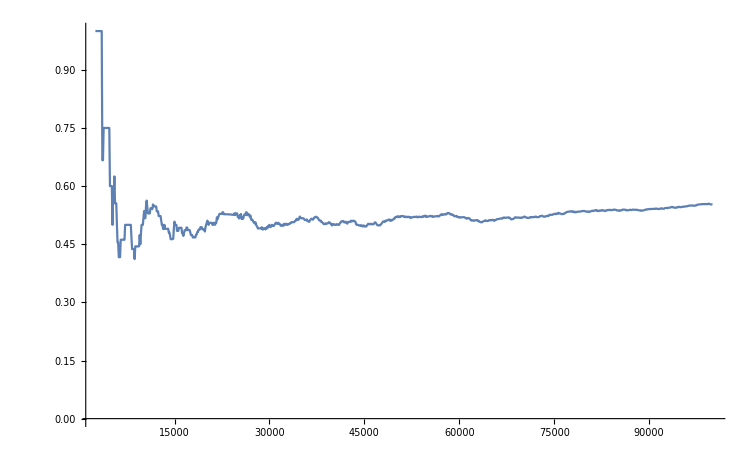

```mathematica
ListLinePlot[data, PlotRange->All]
```

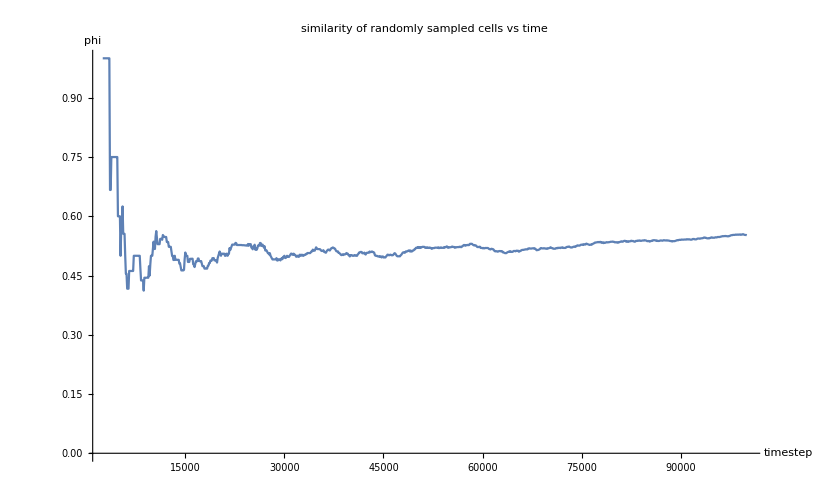

```mathematica
Show[%30,AxesLabel->{HoldForm[timestep],HoldForm[phi]},
PlotLabel->HoldForm[similarity of randomly sampled cells vs time],LabelStyle->{GrayLevel[0]}]
```